# Trust Region Approximations

Our book discusses various approximate solutions for the standard trust region problem
	p^*=argmin_(||p||≤Δ)0.5p.B.p+g.p
we want to compare these to the GEV algorithm.  The overall aim is to get a decent approximation reasonably cheaply.  All of them will check for a feasible internal min. The directions that are available are -g the steepest descent direction and -B^-1g the Newton step.

The simplest step is “steepest descent” but in the trust region language it is the Cauchy point
	p_C=-g/(||g||)Δ

Our book next discusses dogleg steps. Dogleg steps leave the origin in the steepest descent direction if they hit a minimum before they hit the boundary they turn and head to the Newton point p_N=-A^-1g.  They stop when they hit the boundary.

Two D minimization scheme computes an accurate solution (satisfying the constraint) over the 2D span 
	sp{p_C,p_N}.
This algorithm is a 2D version of the GEV algorithm!

Section 4.3 discusses a more ambitious approximation technique. First note that 
	p(λ)= -(B+λ I)^-1.g with ||p(λ)||=Δ
for some λ>0 with B+λ I≻0 unless there is an internal critical point.

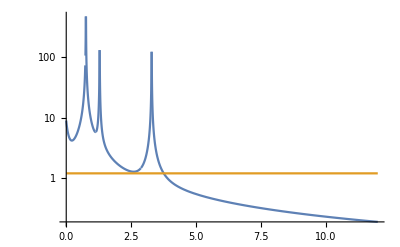

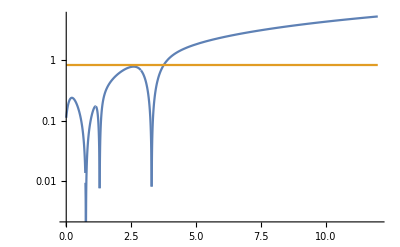

```mathematica
n=7;
B=RandomReal[{-1,1},{n,n}]; B = B + Bᵀ;
g=RandomReal[{-1,1},n];
Δ=1.2;
LogPlot[ {Norm[ LinearSolve[B+ λ IdentityMatrix[n],-g]],Δ},{λ,0, 12},PlotRange->All]
LogPlot[ {1/Norm[ LinearSolve[B+ λ IdentityMatrix[n],-g]],1/Δ},{λ,0, 12},PlotRange->All]
```